```mathematica
(* This solution uses its own stat mech equations. It does not rely on G16 to compute theromodyanmic functions. It only takes  electronic energies, moments of inertia, and vibrational frequencies from G16 *)
```

```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* constants/conversion, SI units unless specified *)
hPlank=6.626070040*10^-34; (* plank constant *)
hbar=hPlank/(2 π);
c0=299792458; (* speed of light *)
kB=1.38064852*10^-23; (* boltzmann constant *)
NA=6.022140857*10^23; (* avogadro's constant *)
Rg=kB*NA; (* gas constant *)

h2j=4.35974 10^-18;(* hartree to joule *)
amu2kg=1.660539040*10^-27; (* atomic mass to kg *)
atm2Pa=101325; (* atm to pascal *)
h2kjmol=2625.499638; (* hartree to kJ/mol *)
h2jmol=2625499.638; (* hartree to J/mol *)
MIau2kgm2=amu2kg*(5.29177×10^-11)^2; (* moment of inertia au to kg.m2 *)
```

```mathematica
(* MAIN EQUATIONS, SI units *)

(* q translational *)
Qtran[M_,T_,P_]:=((kB T)/P)((2 π M kB T)/hPlank^2)^(3/2) ;

(* q rotational *)
Qrot[MI_,T_,sig_]:=Sqrt[π]/sig((8 π^2 kB T)/hPlank^2)^(3/2)Sqrt[Apply[Times,MI]];

(* q vibrational, freq must be in sec^(-1) *)
Qvib[freq_,T_]:=Apply[Times,Exp[-(freq hPlank)/(2kB T)]]/Apply[Times,1-Exp[-(freq hPlank)/(kB T)]];

(* q electronic, make sure that energies of molecules refer to the same zero level. normally this means that the same method and basis sets are used *)
Qelec[Egs_,Wgs_,T_]:=Wgs Exp[-Egs/(kB T)]

(* Internal energy *)
VibE[x_,T_]=hPlank(x/2+x/(Exp[hPlank x/(kB T)]-1));
TranE[T_]=kB T 3/2;
RotE[T_]=kB T 3/2;
(* Many-atom molecule *)
En[freq_,Egs_,T_]:=Egs+RotE[T]+TranE[T]+ Total[VibE[#,T]&/@freq];
(* Single atom/ion does not have rotations and vibrations *)
EnAtom[Egs_,T_]:=Egs+TranE[T];

(* Enthalpy *)
H[freq_,Egs_,T_]:=En[freq,Egs,T]+kB T
HAtom[Egs_,T_]:=EnAtom[Egs,T]+kB T

(* Helmholtz free energy *)
A[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs]+Log[Qrot[MI,T,sig]]+Log[Qvib[freq,T]])+Egs
AAtom[M_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs])+Egs

(* Gibbs free energy *)
G[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=A[M,MI,sig,freq,Egs,Wgs,T,P]+kB T
GAtom[M_,Egs_,Wgs_,T_,P_]:=AAtom[M,Egs,Wgs,T,P]+kB T
```

```mathematica
(* Molecular characteristic, can be found in G16 output files *)

(* A *)
Print["Molecule A"];
MA =120.05751*amu2kg; (* molecular mass *)
MIA={491.06029,1488.22724,1968.09311}*MIau2kgm2; (* moments of inertia *)
(* to extract frequencies use bash: 

awk '/Frequencies/{printf("%.4f,%.4f,%.4f,",$3,$4,$5)}' filename.log

*)
FreqA={61.4748,153.5077,181.1399,231.0419,374.8193,413.5308,431.8786,469.5484,597.9076,603.9536,629.7564,704.3354,744.3933,778.5429,866.6412,952.1156,966.2871,993.0903,1014.5376,1015.8875,1046.3347,1049.9012,1099.5394,1118.6551,1193.1573,1212.3069,1284.7447,1345.4749,1365.5327,1393.9602,1475.6714,1480.9257,1487.3051,1533.6670,1631.6097,1651.7980,1751.4033,3051.0795,3116.6921,3166.2512,3186.3179,3196.0131,3205.8155,3216.1683,3218.8833}*c0*100;
SigmaA=1; (* rotational symmetry *)
ElectronicA=-384.925582213*h2j; (* electronic energy *)

(* BH2 *)
Print["Molecule BH2"];
MBH2 =32.03745*amu2kg;
MIBH2={12.74031,74.53486,75.25956}*MIau2kgm2;
FreqBH2={406.8851,866.7245,1058.5823,1130.3892,1304.3368,1359.0564,1673.9638,1686.2768,3427.8544,3441.2439,3538.7493,3549.0595}*c0*100;
SigmaBH2=1;
ElectronicBH2=-111.877372912*h2j;

(* A..BH2 *)
Print["Molecule A..BH2"];
MAdotBH2 =152.094965*amu2kg;
MIAdotBH2={661.38957,3901.09319,4284.62788}*MIau2kgm2;
FreqAdotBH2={20.1871,40.0810,64.8942,85.6257,115.4994,136.3181,159.0293,194.8579,218.7098,250.9675,384.1205,413.6229,428.2678,434.0549,478.8419,604.3023,606.7015,629.6497,703.2442,747.6021,779.2180,866.1455,884.1093,954.0285,970.6134,993.8991,1014.5170,1017.1183,1047.9706,1050.7324,1091.6120,1105.1607,1121.1038,1153.0810,1194.8304,1214.7726,1291.9883,1334.9737,1347.2206,1356.1881,1367.0435,1399.9266,1481.4413,1487.5898,1489.2897,1534.5127,1630.7649,1651.2941,1676.5145,1692.4664,1736.6872,3053.9272,3118.6869,3172.5453,3187.3786,3197.4968,3206.9963,3217.8523,3220.4013,3441.0290,3445.4715,3530.8850,3538.2936}*c0*100;
SigmaAdotBH2=1;
ElectronicAdotBH2=-496.812913388*h2j;

(* transition state *)
Print["Transition state AH..BH..A"];
MTSAHdotBHdotA =272.15248*amu2kg;
MITSAHdotBHdotA={5164.44541,5647.43255,8865.25308}*MIau2kgm2;
FreqTSAHdotBHdotA={21.5188,25.6770,54.2057,62.7413,71.5964,82.7708,97.8592,115.5795,165.7377,214.7462,223.3021,234.9894,245.2619,255.7787,261.1133,268.3639,274.0937,298.4557,312.6126,363.4498,371.4836,395.3618,418.3963,428.8869,459.5593,479.5181,485.6124,529.8392,552.4157,569.4684,615.6573,626.1073,630.4823,631.6815,704.8423,709.9152,722.7036,756.2738,773.9493,782.4237,841.4907,853.1974,860.9678,924.9974,932.6076,942.0503,966.9800,978.8028,982.6357,1000.6524,1003.2875,1005.9805,1007.1174,1011.6115,1048.2585,1050.1404,1057.7670,1070.0645,1088.0063,1093.2882,1107.6934,1111.6828,1130.6464,1188.5296,1190.5620,1210.9624,1214.4373,1229.2297,1240.2365,1285.7283,1294.3842,1337.7197,1345.3087,1361.3945,1365.7802,1376.4917,1404.1283,1414.5563,1421.5722,1483.2336,1486.8224,1491.1694,1498.5523,1501.1906,1512.0509,1521.3238,1533.5351,1535.7419,1615.4443,1625.1232,1642.3623,1648.2180,1757.5429,1988.8154,3034.7413,3035.9223,3113.4837,3115.1055,3162.9985,3165.1759,3177.7261,3179.7783,3186.3781,3187.7879,3201.5288,3203.5913,3219.7142,3224.4518,3225.0828,3226.7670,3385.1921,3528.5612,3536.7230}*c0*100;
SigmaTSAHdotBHdotA=1;
ElectronicTSAHdotBHdotA=-881.659377969*h2j;
```

Molecule A

Molecule BH2

Molecule A..BH2

Transition state AH..BH..A

```mathematica
KeqT={};
KrateT={};
Do[
Do[

Print[];
Print["===================="];
Style[Print["Temperature (Kelvin) and pressure (atm) = ",T0,", ",P0],Red];


Print["Molecule A"];
(* calculate thermodynamic funtions at 400 K and 2 atm *)
QA=Qtran[MA,T0,P0*atm2Pa]Qrot[MIA,T0,1]Qvib[FreqA,T0];
(* evaluate electronic partition function separately, note that this is a gigantic number, cannot be computed in G16 *)
Print["Correct electronic partition function = ",Qelec[ElectronicA,1,T0] ];
(* Gibbs free energy *)
GA=G[MA,MIA,SigmaA,FreqA,ElectronicA,1,T0,P0*atm2Pa];
(* Compute correction to compare with G16 output *)
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GA-ElectronicA)/h2j, " hartree"];
(* Helmholtz free energy *)
AA=A[MA,MIA,SigmaA,FreqA,ElectronicA,1,T0,P0*atm2Pa];
(* Internal energy *)
EA=En[FreqA,ElectronicA,T0];
(* Enthalpy *)
HA=H[FreqA,ElectronicA,T0];



Print["Molecule BH2"];QBH2=Qtran[MBH2,T0,P0*atm2Pa]Qrot[MIBH2,T0,1]Qvib[FreqBH2,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicBH2,1,T0] ];
GBH2=G[MBH2,MIBH2,SigmaBH2,FreqBH2,ElectronicBH2,1,T0,P0*atm2Pa];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GBH2-ElectronicBH2)/h2j, " hartree"];
ABH2=A[MBH2,MIBH2,SigmaBH2,FreqBH2,ElectronicBH2,1,T0,P0*atm2Pa];
EBH2=En[FreqBH2,ElectronicBH2,T0];
HBH2=H[FreqBH2,ElectronicBH2,T0];



Print["Molecule A..BH2"];QAdotBH2 =Qtran[MAdotBH2 ,T0,P0*atm2Pa]Qrot[MIAdotBH2 ,T0,1]Qvib[FreqAdotBH2 ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAdotBH2 ,1,T0] ];
GAdotBH2 =G[MAdotBH2 ,MIAdotBH2 ,SigmaAdotBH2 ,FreqAdotBH2 ,ElectronicAdotBH2 ,1,T0,P0*atm2Pa];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAdotBH2 -ElectronicAdotBH2 )/h2j, " hartree"];
AAdotBH2 =A[MAdotBH2 ,MIAdotBH2 ,SigmaAdotBH2 ,FreqAdotBH2 ,ElectronicAdotBH2 ,1,T0,P0*atm2Pa];
EAdotBH2 =En[FreqAdotBH2 ,ElectronicAdotBH2 ,T0];
HAdotBH2 =H[FreqAdotBH2 ,ElectronicAdotBH2 ,T0];




Print["Transition state AH..BH..A"];QTSAHdotBHdotA =Qtran[MTSAHdotBHdotA ,T0,P0*atm2Pa]Qrot[MITSAHdotBHdotA ,T0,1]Qvib[FreqTSAHdotBHdotA ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicTSAHdotBHdotA ,1,T0] ];
GTSAHdotBHdotA =G[MTSAHdotBHdotA ,MITSAHdotBHdotA ,SigmaTSAHdotBHdotA ,FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,1,T0,P0*atm2Pa];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GTSAHdotBHdotA -ElectronicTSAHdotBHdotA )/h2j, " hartree"];
ATSAHdotBHdotA =A[MTSAHdotBHdotA ,MITSAHdotBHdotA ,SigmaTSAHdotBHdotA ,FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,1,T0,P0*atm2Pa];
ETSAHdotBHdotA =En[FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,T0];
HTSAHdotBHdotA =H[FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,T0];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction: A + BH2 <-> A..BH2"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAdotBH2-ElectronicA - ElectronicBH2)*NA;
(* Internal E, J/mol *)
DeltaE=(EAdotBH2-EA-EBH2)*NA;
(* Enthalpy change *)
DeltaH=(HAdotBH2-HA-HBH2)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAdotBH2-GA-GBH2)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAdotBH2-AA-ABH2)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];
Print[];

(* Equilibrium constant *)
(*
(* use partition functions, V0 is fake volume, it is shown here as a reminder *)
V0 =1;
Keq1 = (QP1/V0)/(QR/V0)Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",Keq1];

(* now use gibbs free energy to get the same constant *)
(* this expression is valid only for reactions with Delta N = 0 *)
Keq2=Exp[-DeltaG/(NA kB T0)];

Print["Use reaction free energy. Equilibrium constant = ",Keq2];

KeqT=Append[KeqT,{T0,Keq2}];


(* Rate constant *)

Print["Solution D."];

Krate1 =(kB T0)/hPlank Exp[-(ElectronicT-ElectronicR)/(kB T0)]((QT/V0)/(QR/V0));

Print["Use partition functions. Rate constant = ",Krate1," s^(-1)"];
Krate2 =(kB T0)/hPlank Exp[-(GT-GR)/(kB T0)];
Print["Use activation free energy. Rate constant = ",Krate2," s^(-1)"];

(* save current temperature data into a list: 1/RT vs. Log K_rate *)
KrateT=Append[KrateT,    {1/(kB NA T0),Log[Krate2]}    ];
*)

Print["Done with temperature/pressure: ",T0, ", ",P0];
Print["===================="];

,{T0,298,298,10}]
,{P0,1,10,1}]
 (* Temperature (Kelvin) and pressure (atm) *)
```

====================

Temperature (Kelvin) and pressure (atm) = 298, 1

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.105565 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0307837 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.152891 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.279451 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 19763.6

Delta G = 17285.9

Entropy units are J/mol/K.

Delta S = -123.556

Done with temperature/pressure: 298, 1

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 2

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.10622 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0314378 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.153545 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.280105 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 18046.2

Delta G = 15568.5

Entropy units are J/mol/K.

Delta S = -117.793

Done with temperature/pressure: 298, 2

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 3

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.106602 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0318205 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.153928 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.280488 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 17041.6

Delta G = 14563.9

Entropy units are J/mol/K.

Delta S = -114.422

Done with temperature/pressure: 298, 3

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 4

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.106874 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.032092 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.1542 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.280759 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 16328.8

Delta G = 13851.1

Entropy units are J/mol/K.

Delta S = -112.03

Done with temperature/pressure: 298, 4

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 5

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.107084 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0323026 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.15441 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.28097 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 15775.9

Delta G = 13298.2

Entropy units are J/mol/K.

Delta S = -110.175

Done with temperature/pressure: 298, 5

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 6

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.107256 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0324746 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.154582 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.281142 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 15324.2

Delta G = 12846.5

Entropy units are J/mol/K.

Delta S = -108.659

Done with temperature/pressure: 298, 6

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 7

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.107402 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0326201 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.154728 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.281288 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 14942.2

Delta G = 12464.5

Entropy units are J/mol/K.

Delta S = -107.377

Done with temperature/pressure: 298, 7

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 8

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.107528 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0327461 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.154854 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.281414 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 14611.4

Delta G = 12133.7

Entropy units are J/mol/K.

Delta S = -106.267

Done with temperature/pressure: 298, 8

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 9

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.107639 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0328573 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.154965 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.281525 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 14319.6

Delta G = 11841.9

Entropy units are J/mol/K.

Delta S = -105.288

Done with temperature/pressure: 298, 9

====================

====================

Temperature (Kelvin) and pressure (atm) = 298, 10

Molecule A

Correct electronic partition function = 1.998727077×10^177142

Sanity check. Compare to G16 output. G thermal correction = 0.107738 hartree

Molecule BH2

Correct electronic partition function = 6.848400993×10^51485

Sanity check. Compare to G16 output. G thermal correction = 0.0329567 hartree

Molecule A..BH2

Correct electronic partition function = 5.237494886×10^228632

Sanity check. Compare to G16 output. G thermal correction = 0.155064 hartree

Transition state AH..BH..A

Correct electronic partition function = 4.07413863×10^405738

Sanity check. Compare to G16 output. G thermal correction = 0.281624 hartree

Reaction: A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17056.1

Delta H = -19533.8

Delta A = 14058.5

Delta G = 11580.8

Entropy units are J/mol/K.

Delta S = -104.411

Done with temperature/pressure: 298, 10

====================

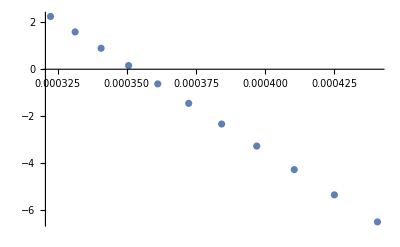

```mathematica
(* Arrhenius plot *)
ListPlot[KrateT]
```